## Stresses under mixed-mode loading

```mathematica
σxx=1/(√(2π*r))(KI*Cos[θ/2]*(1-Sin[θ/2]*Sin[(3*θ)/2])-KII*Sin[θ/2]*(2+Cos[θ/2]*Cos[(3*θ)/2]));
σyy=1/(√(2π*r))(KI*Cos[θ/2]*(1+Sin[θ/2]*Sin[(3*θ)/2])+KII*Sin[θ/2]*Cos[θ/2]*Cos[(3*θ)/2]);
τxy=1/(√(2π*r))(KI*Sin[θ/2]*Cos[θ/2]*Cos[(3*θ)/2]+KII*Cos[θ/2]*(1-Sin[θ/2]*Sin[(3*θ)/2]));
τxz=-KIII/(√(2π*r))*Sin[θ/2];τyz=KIII/(√(2π*r))*Cos[θ/2];
```

plain strain

```mathematica
σzz=ν*(σxx+σyy);
```

plain stress

```mathematica
σzz=0;
```

## Mises yield function

```mathematica
σM=√(1/2*((σxx-σyy)^2+(σyy-σzz)^2+(σzz-σxx)^2+6*(τxy^2+τyz^2+τxz^2)));
```

## Crack-tip plastic zone

plain strain

```mathematica
TrigExpand@TrigReduce[Reduce[σM==Sqrt[3/(8π)],r]/.{KI->1,KII->0,KIII->0}]
```

7/8-2 ν+2 ν^2+Cos[θ]/2-2 ν Cos[θ]+2 ν^2 Cos[θ]-(3 Cos[θ]^2)/8+(3 Sin[θ]^2)/8≠0&&r==7/6-(8 ν)/3+(8 ν^2)/3+(2 Cos[θ])/3-8/3 ν Cos[θ]+8/3 ν^2 Cos[θ]-Cos[θ]^2/2+Sin[θ]^2/2

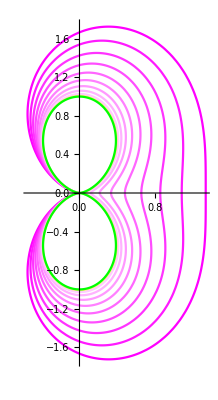

```mathematica
Show[Table[PolarPlot[7/6-(8 ν)/3+(8 ν^2)/3+(2 Cos[θ])/3-8/3 ν Cos[θ]+8/3 ν^2 Cos[θ]-Cos[θ]^2/2+Sin[θ]^2/2,{θ,0,2Pi},PlotStyle->RGBColor[10-20ν,2ν,5-10ν]],{ν,0,0.5,0.05}]]
```

19/8-2 ν+2 ν^2-Cos[θ]/2+2 ν Cos[θ]-2 ν^2 Cos[θ]+(9 Cos[θ]^2)/8-(9 Sin[θ]^2)/8≠0&&r==19/6-(8 ν)/3+(8 ν^2)/3-(2 Cos[θ])/3+8/3 ν Cos[θ]-8/3 ν^2 Cos[θ]+(3 Cos[θ]^2)/2-(3 Sin[θ]^2)/2

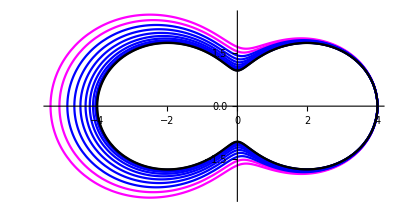

```mathematica
TrigExpand@TrigReduce[Reduce[σM==Sqrt[3/(8π)],r]/.{KI->0,KII->1,KIII->0}]
Show[Table[PolarPlot[19/6-(8 ν)/3+(8 ν^2)/3-(2 Cos[θ])/3+8/3 ν Cos[θ]-8/3 ν^2 Cos[θ]+(3 Cos[θ]^2)/2-(3 Sin[θ]^2)/2,{θ,0,2Pi},PlotStyle->RGBColor[10-100ν,-ν,5-10ν]],{ν,0,0.5,0.05}]]
```